# Useful Formulas

Formulas that you should know and love!

### Special Relativity

#### Time Dilation

```mathematica
Grid[{{-Graphics-,-Graphics-}},Spacings->{5, 1}]
```

-Graphics- | -Graphics-

Frame A moves at velocity v relative to frame B. Two events occur at the same location in frame A, separated by a time t_A. In frame B, these two events are separated by a time

t_B=γ t_A

where

γ≡1/(√(1-(v/c)^2))

t_A (the shortest possible time separation in any reference frame) is called the proper time of these two events.

#### Head Start Effect

Two clocks are synchronized in a moving train’s frame. When both clocks are observed simultaneously from the ground frame, the rear clock is ahead by a time

Δ,t=(L v)/c^2

Additionally, each of these two clocks also tick at a slower rate (of γ) relative to the ground’s clock, but because both clocks tick at this slower rate their time difference Δ,t=(L v)/c^2 continues to holds.

#### Length Contraction

```mathematica
Grid[{{-Graphics-,-Graphics-}},Spacings->{5, 1}]
```

-Graphics- | -Graphics-

A train moves at speed v relative to the ground. A stationary observer in the train’s frame measures the train to be length l'. A stationary observer in the ground’s frame measures the train to be length

l=l'/γ

where

γ≡1/(√(1-(v/c)^2))

l' (the longest possible length in any reference frame) is called the proper length of the train.

#### Lorentz Transformation

Δ,x=γ (Δ,x'+v Δ,t')
Δ,t=γ (Δ,t'+v/c^2 Δ,x')
Δ,y=Δ,y'
Δ,z=Δ,z'

```mathematica
f=Style[#,FontFamily->"Times"]&;
g=Style[#,FontFamily->"Times",Bold]&;
Grid[{g/@{"Effect","Condition","Result"},{f@"Time Dilation","Δ,x'=0","Δ,t = γ Δ,t'"},{f@"Length Contraction","Δ,t'=0","Δ,x' = Δ,x/γ"},{f@"Relative v of Frames","Δ,x=0","Δ,x' = -v Δ,t"},{f@"Head Start Effect","Δ,t=0","Δ,t' = -v Δ,x'/c^2"}},Frame->All]
```

Effect | Condition | Result
Time Dilation | Δ,x'=0 | Δ,t = γ Δ,t'
Length Contraction | Δ,t'=0 | Δ,x' = Δ,x/γ
Relative v of Frames | Δ,x=0 | Δ,x' = -v Δ,t
Head Start Effect | Δ,t=0 | Δ,t' = -v Δ,x'/c^2

#### Velocity Addition

Velocity addition along one axis. What is the speed, u, of the object with respect to frame S?

u=(v_1+v_2)/(1+(v_1 v_2)/c^2)

#### Energy and Momentum

p⃗=γ m v⃗

E=γ m c^2

which have the very important relation

E^2=p^2 c^2+m^2 c^4

Lorentz transformation of energy and momentum

E/c=γ (E'/c+v/c p')

p=γ (p'+v/c^2 E')

### Electrostatics

#### Coulomb Force

F⃗=k(q_1 q_2)/r_21^2(r̂)_21

k=1/(4π ϵ_0)=9×10^9(N·m^2)/C^2

#### Electric Field, Electric Potential, Charge Density

```mathematica
θ1=π/2;θ2=π/2+2π/3;θ3=π/2+4π/3;
p1={Cos[θ1],Sin[θ1]};p2={Cos[θ2],Sin[θ2]};p3={Cos[θ3],Sin[θ3]};
ft=Style[#,16,FontFamily->"Times New Roman"]&;
ft2=Style[#,14,FontFamily->"Times New Roman"]&;
s2=0.17;s3=0.9;
Graphics[{Circle[#,0.2]&/@{p1,p2,p3},Text[ft@"ρ",p1],Text[ft@"ϕ",p2],Text[ft@"E⃗",p3],Arrow[1.1{{p1+s2(p2-p1),p2-s2(p2-p1)},{p3+s2(p2-p3),p2-s2(p2-p3)},{p1+s2(p3-p1),p3-s2(p3-p1)}}],Arrow[0.9{{p1+s3(p2-p1),p2-s3(p2-p1)},{p3+s3(p2-p3),p2-s3(p2-p3)},{p1+s3(p3-p1),p3-s3(p3-p1)}}],Text[ft2@"E⃗=-OverVector[∇]ϕ",(p2+p3)/2+{0,0.15}],Text[ft2@"ϕ=-∫E⃗·ⅆ s⃗",(p2+p3)/2-{0,0.17}],Text[Rotate[ft2@"∇^2 ϕ=-ρ/ϵ_0",Pi/3],(p1+p2)/2+{0.13,-0.18}],Text[Rotate[ft2@"ϕ=∫(k ⅆq)/r",Pi/3],(p1+p2)/2+{-0.166,0.062}],Text[Rotate[ft2@"E⃗=∫(k ⅆq)/r^2 r̂",-Pi/3],(p1+p3)/2+{0.172,0.09}],Text[Rotate[ft2@"OverVector[∇]·E⃗=ρ/ϵ_0,OverVector[∇]×E⃗=OverVector[0]",-Pi/3],(p1+p3)/2+{-0.126,-0.15}]},ImageSize->200]
```

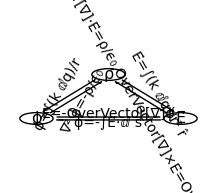

#### Energy

The potential energy required to bring a system of N point charges from infinity,

U=1/2∑_(j=1)^N ∑_(k≠j) (k q_j q_k)/(r_(j,k))

For a continuous charge distribution

U=ϵ_0/2∫E^2 ⅆv=1/2∫ρ ϕⅆv

#### Conductors

E⃗=0 inside a conductor

ρ=0 inside a conductor

Any net charge resides on the surface

A conductor surface is equipotential

E⃗ is perpendicular to the surface, just outside a conductor

#### Capacitors

Energy

U=1/2 C V^2=1/2 Q V=Q^2/(2C)

### Electrodynamics

#### Circuits

Voltage drop across circuit element with resistance R,

V=I R

Power delivered to circuit element at potential difference V with current I flowing through,

P=I V=I^2 R

When analyzing circuits to find how they behave with respect to time, write every circuit element using its associated charge Q using

Q=C V

I=V/R

I=-ⅆQ/ⅆt

#### Circuit Elements

Resistors

1/R_parallel=1/R_1+1/R_2+···+1/R_n

R_series=R_1+R_2+···+R_n

Capacitors

C_parallel=C_1+C_2+···+C_n

1/C_series=1/C_1+1/C_2+···+1/C_n

### Physical Constants

Charge of an electron e=1.6 10^-19 C
Mass of an electron m_e=9.1 10^-31 kg
Speed of light c=1/(ϵ_0 μ_0)^(1/2)=3 10^8 m/s
Coulomb constant k=9 10^9(N m^2)/C^2
Permittivity of free space ϵ_0=8.85 10^-12 C^2/(N m^2)
Permeability of free space μ_0=4π·10^-7(V·s)/(A·m)=1.3 10^-6 N/A^2

### Math

#### Dot and Cross Product

Given vectors A⃗=A_x î+A_y ĵ+A_z k̂ and B⃗=B_x î+B_y ĵ+B_z k̂ with angle θ between them,

A⃗·B⃗=A_x B_x+A_y B_y+A_z B_z=|A⃗||B⃗|Cos[θ]

A⃗×B⃗=(A_y B_z-A_z B_y)î+(A_z B_x-A_x B_z)ĵ+(A_x B_y-A_y B_x)k̂=|A⃗||B⃗|Sin[θ]n̂

where n̂ is a unit vector given applying the right-hand rule to A⃗ and B⃗. A useful mnemonic to remember the cross product is

A⃗×B⃗=|î | ĵ | k̂
A_x | A_y | A_z
B_x | B_y | B_z|

#### Derivatives and Integrals

ⅆ/ⅆx[y+z]=ⅆy/ⅆx+ⅆz/ⅆx
ⅆ/ⅆx[y z]=ⅆy/ⅆx z+y ⅆz/ⅆx
ⅆy/ⅆt=ⅆy/ⅆx ⅆx/ⅆt

ⅆ/ⅆx[x^n]=n x^(n-1)
ⅆ/ⅆx[ⅇ^(b x)]=b ⅇ^(b x)
ⅆ/ⅆx[Sin[b x]]=b Cos[b x]
ⅆ/ⅆx[Cos[b x]]=-b Sin[b x]
ⅆ/ⅆx[Log[b x]]=1/x

#### Trig Functions

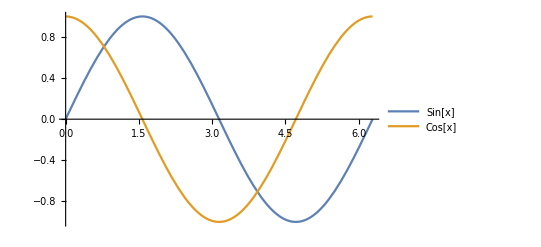

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π},PlotLegends->{"Sin[x]","Cos[x]"}]
```

Sin[x]=x-x^3/(3!)+x^5/(5!)-···=∑_(j=0)^∞ (-1)^j x^(2j+1)/((2j+1)!)=(ⅇ^(ⅈ x)-ⅇ^(-ⅈ x))/(2ⅈ)
Cos[x]=1-x^2/(2!)+x^4/(4!)-···=∑_(j=0)^∞ (-1)^j x^(2j)/((2j)!)=(ⅇ^(ⅈ x)+ⅇ^(-ⅈ x))/2

Sin[x+y]=Sin[x]Cos[y]+Cos[x]Sin[y]
Cos[x+y]=Cos[x]Cos[y]-Sin[x]Sin[y]

Sin[2x]=2Sin[x]Cos[x]
Cos[2x]=Cos[x]^2-Sin[x]^2=2 Cos[x]^2-1=1-2 Sin[x]^2

Sin[π-x]=Sin[x]
Cos[π-x]=-Cos[x]

Cos[0]=1 |  |  | Sin[0]=0
Cos[π/6]=(√3)/2 |  |  | Sin[π/6]=1/2
Cos[π/4]=(√2)/2 |  |  | Sin[π/4]=(√2)/2
Cos[π/3]=1/2 |  |  | Sin[π/3]=(√3)/2
Cos[π/2]=0 |  |  | Sin[π/2]=1

### Coordinate systems

#### Spherical Coordinates

```mathematica
arc[r_,θ_,{ϕ1_, ϕ2_}]:=
Line[Table[r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{ϕ,ϕ1,ϕ2,(ϕ2-ϕ1)/Round[((ϕ2-ϕ1)/(2π))180.]}]]
arc[r_,{θ1_,θ2_},ϕ_]:=
Line[Table[r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
PolarToCartesian[{r_,θ_,ϕ_}]:=
r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]}
sphericalGraphic = With[{hemisphere = First[ParametricPlot3D[
{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{ϕ,0,π/2},{θ,0,2π},Boxed->False,Mesh->None,Axes->None]],
al=1.2,
tl=1.3
},
Graphics3D[{
Arrowheads[Small],
Arrow[al{{{-1,0,0},{1,0,0}},{{0,-1,0},{0,1,0}},{{0,0,-.1/1.1},{0,0,1}}}],
Text["x",tl{1,0,0}],
Text["y",tl{0,1,0}],
Text["z",tl{0,0,1}],
With[{ϕ=45°,θ=45°,ar=.25,tr=.35},
{
{Arrow[{{0,0,0},PolarToCartesian[{1,θ,θ}]}]},
arc[1,ϕ,{0,θ}],
arc[Sin[θ],{0,ϕ},π/2],
Line[{{0,0,0},PolarToCartesian[{Sin[θ],ϕ,π/2}],
PolarToCartesian[{1,ϕ,θ}]}],
arc[ar,{0,ϕ},π/2],
arc[ar,ϕ,{0,θ}],
Text["ϕ",PolarToCartesian[{tr,ϕ/2,π/2}],{-1,1}],
Text["θ",PolarToCartesian[{tr,θ,θ/2}],{0,-1}]
}],
{Opacity[.5],hemisphere}
},Boxed->False,ViewPoint->{2.72,-0.92,1.78},ViewVertical->{0.07,-0.037,1.83}]
];
polarGraphic = With[{disk = First[ParametricPlot3D[
{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], 0},{ϕ,0,π/2},{θ,0,2π},Boxed->False,Mesh->None,Axes->None]],
al=1.2,
tl=1.3
},
Graphics3D[{
Arrowheads[Small],
{Style[Text["z",tl{0,0,1}],FontOpacity->0]},
Arrow[al{{{-1,0,0},{1,0,0}},{{0,-1,0},{0,1,0}}}],
Text["x",tl{1,0,0}],
Text["y",tl{0,1,0}],
With[{θ=45°,ϕ=45°,ar=.25,tr=.35},
{
arc[ar,{0,θ},π/2],
Arrow[{{0,0,0},PolarToCartesian[{Sin[ϕ],θ,π/2}]}],
Text["θ",PolarToCartesian[{tr,θ/2,π/2}],{-1,1}],
Text["r",PolarToCartesian[{.4,θ,π/2}],{-1,-1}]
}],
{Opacity[.7],disk}
},Boxed->False,ViewPoint->{2.72,-0.92,1.78},ViewVertical->{0.07,-0.037,1.83}]
];
Row[Show[#,ImageSize->200]& /@ {sphericalGraphic}]
```

-Graphics3D-

Spherical to Cartesian - Coordinates

x=r Sin[θ]Cos[ϕ]
y=r Sin[θ]Sin[ϕ]
z=r Cos[θ]

Spherical to Cartesian - Unit Vectors

x̂=Sin[θ]Cos[ϕ]r̂+Cos[θ]Cos[ϕ]θ̂-Sin[ϕ]ϕ̂
ŷ=Sin[θ]Sin[ϕ]r̂+Cos[θ]Sin[ϕ]θ̂+Cos[ϕ]ϕ̂
ẑ=Cos[θ]r̂-Sin[θ]θ̂

Cartesian to Spherical - Coordinates

r=√(x^2+y^2+z^2)
θ=ArcTan[((x^2+y^2)^(1/2))/z]
ϕ=ArcTan[y/x]

Cartesian to Spherical - Unit Vectors

r̂=Sin[θ]Cos[ϕ]x̂+Sin[θ]Sin[ϕ]ŷ+Cos[θ]ẑ
θ̂=Cos[θ]Cos[ϕ]x̂+Cos[θ]Sin[ϕ]ŷ-Sin[θ]ẑ
ϕ̂=-Sin[ϕ]x̂+Cos[ϕ]ŷ

Volume integrals

spherical coordinate volume element=r^2 Sin[θ]ⅆrⅆθⅆϕ

#### Cylindrical Coordinates

Cylindrical to Cartesian - Coordinates

x=ρ Cos[ϕ]
y=ρ Sin[ϕ]
z=z

Cylindrical to Cartesian - Unit Vectors

x̂=Cos[ϕ]ρ̂-Sin[ϕ]ϕ̂
ŷ=Sin[ϕ]ρ̂+Cos[ϕ]ϕ̂
ẑ=ẑ

Cartesian to Cylindrical - Coordinates

ρ=√(x^2+y^2)
ϕ=ArcTan[y/x]
z=z

Cartesian to Cylindrical - Unit Vectors

ρ̂=Cos[ϕ]x̂+Sin[ϕ]ŷ
ϕ̂=-Sin[ϕ]x̂+Cos[ϕ]ŷ
ẑ=ẑ

Volume integrals

cylindrical coordinate volume element=ρⅆρⅆθⅆz